```mathematica
x={35,42,79,144}
```

{35,42,79,144}

```mathematica
y={37,36,73,154}
```

{37,36,73,154}

```mathematica
nx=Total[x]
```

300

```mathematica
ny=Total[y]
```

300

```mathematica
(*Эмпирическое среднее f1*)
```

```mathematica
N[ax=1/nx∑_(i=1)^Length[x] (i+1) x[[i]]]
```

4.10667

```mathematica
(*Эмпирическое среднее f2*)
```

```mathematica
N[ay=1/ny∑_(i=1)^Length[y] (i+1) y[[i]]]
```

4.14667

```mathematica
(*Эмпирическая дисперсия f1*)
```

```mathematica
N[σx=√(1/nx∑_(i=1)^Length[x] (i+1-a)^2 x[[i]])]
```

1.03696

```mathematica
(*Эмпирическая дисперсия f2*)
```

```mathematica
N[σy=√(1/ny∑_(i=1)^Length[y] (i+1-a)^2 y[[i]])]
```

1.05202

```mathematica
(*График модуля разности f1 и f2*)
```

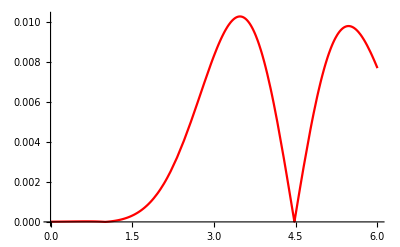

```mathematica
Plot[Abs[PDF[NormalDistribution[ax,σx],x]-PDF[NormalDistribution[ay,σy],x]],{x,0,6},PlotStyle->{Red,Thickness[0.004]},PlotRange->All]
```

```mathematica
(*Статистика*)
```

```mathematica
t=FindMaximum[Abs[PDF[NormalDistribution[ax,σx],τ]-PDF[NormalDistribution[ay,σy],τ]],{τ,3.5}
][[1]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0102808

```mathematica
If[t<1.6449 √((nx+ny)/(nx ny)),"Гипотеза не отвергнута","Гипотеза отвергнута"]
```

Гипотеза не отвергнута